# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
Manipulate[Plot[a Sin[k x+n],{x,-3,3},PlotRange->{{-5,5},{-5,5}},AspectRatio->Automatic],{a,-3,3},{k,-3,3},{n,-3,3}]
(* V funkciji Plot uporabite nastavitvi Range->{-5,5} in AspectRatio->Automatic *)
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(*y_0=-1/k * x_0 + n_0 -> n_0 = y_0+1/k * x_0 *)
ClearAll[x];
Manipulate[
Plot[{k x+n,If[k!=0,-1/k (x-x0)+y0,y0]},{x,-10,10},
PlotRange->{{-10,10},{-10,10}},
AspectRatio->1,PlotStyle->{Blue,Red},
Epilog->{Red,PointSize[Large],Point[{x0,y0}]}
],
{k,-5,5},{n,-5,5},{x0,-5,5},{y0,-5,5}]
```

Null

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
ClearAll[x0]
f[x_]:=(x*(x-2)^2)/(x^2+1)
Manipulate[
Plot[{f[x], f'[x0]*(x-x0)+f[x0]},{x,-10,10}, 
PlotRange->{{-10,10},{-10,10}},
AspectRatio->1,
Epilog->{Red,PointSize[Large],Point[{x0,f[x0]}]}],
{x0,-10,10}
]
```

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

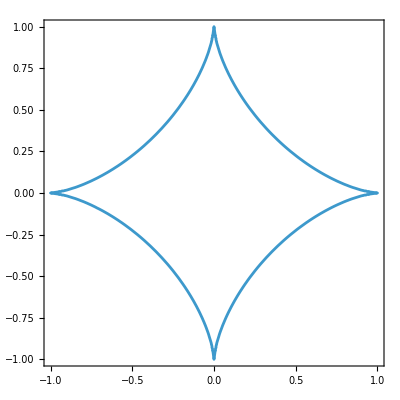

{{p→Log[2]/Log[3]}}

{{p→0.63093}}

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1, {x,-1,1},{y,-1,1}]
Manipulate[
ContourPlot[Abs[x]^(p)+Abs[y]^(p)==1,{x, -2,2},{y,-2,2}],{p,0,4,Initialization:>(p=2)}]
Solve[Abs[1/3]^(p)+Abs[1/3]^(p)==1,p,Reals]
NSolve[Abs[1/3]^(p)+Abs[1/3]^(p)==1,p,Reals]
```

## Vektorji in matrike

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.s
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
v1={1,2,3}
v2={-3,-2,5}
v1.v2
Cross[v1,v2]
If[Norm[v1]> Norm[v2],1,-1,0]
```

{1,2,3}

{-3,-2,5}

8

{16,-14,4}

-1

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
ClearAll[a,b,c]
a={a1,a2,a3}
b={b1,b2,b3}
c={c1,c2,c3}
Reduce[Cross[a,Cross[b,c]]==(a.c)*b-(a.b)*c]
```

{a1,a2,a3}

{b1,b2,b3}

{c1,c2,c3}

True

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
matA={{a11,a12},{a21,a22}}
matB={{b11,b12},{b21,b22}}
Reduce[Inverse[matA.matB]==Inverse[matB].Inverse[matA]]
```

{{a11,a12},{a21,a22}}

{{b11,b12},{b21,b22}}

True

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizabilnost.

```mathematica
M={{9,2,-3},{3,2,1},{6,4,-1}}
Length[M]
Length[M[[1]]] (*stevilo stoplcih*)
Det[M]
evr=Eigenvalues[M]
ev =Eigenvectors[M]
MatrixRank[ev]
If[Length[M]== MatrixRank[M]&& Length[M[[1]]]==MatrixRank[M],1,0]
D=DiagonalMatrix[evr]
P=Transpose[ev]
P1=Inverse[P]
Reduce[P.D.P1==M]
```

{{9,2,-3},{3,2,1},{6,4,-1}}

3

3

-36

{3 (1+√2),4,3 (1-√2)}

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

3

1

Set::wrsym: Symbol D is Protected.

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

{{(7+8/(-1+√2)-(4 √2)/(-1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(-2-8/(-1+√2)+(20 √2)/(3 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(-1+√2)-29/(3 √2 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))},{(-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2 √2)/(3 (-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))},{(-7+8/(1+√2)+(4 √2)/(1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2-8/(1+√2)-(20 √2)/(3 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(1+√2)+29/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))}}

False